# Calculations on MaxEnt

Last updated: Oct28th’21


- The ‘paper’ is Maximal_entanglement_Cervera.pdf
- In the CM frame, if an outgoing particle has angles θ and ϕ, its analog outgoing antiparticle has angle π-θ (insisting that θ lives in [0,π]) and ϕ+π (ϕ=0 only defines the x>0 half-plane!) 
- Adopt the chiral Weyl basis in (2.27) of Giunti’s. [WARNING] It is the negative of Schartz/Peskin chiral basis!).
- In Giunti’s, the “+” and “-” labels in the spinors means RH/LH particles, not spinors
- Giving explicit components to the spinors we find that their entries are real, so no need to complex conjugating them when defining the daggered or the barred ones

```mathematica
SetOptions[EvaluationNotebook[],Background->LightYellow]
SetDirectory[NotebookDirectory[]]
```

/home/carlos/Documents/ResearchUCOL/Quantum/OurPrograms

### LaTeX

LATEX in Mathematica  (assumes equation mode, type for example “x”, “\\log{x}”, “\\text{some text}”. For labels, use Inset[MaTeX[...], Scaled[...]])

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}","\\usepackage[dvipsnames]{xcolor}","\\usepackage{mathtools}",
"\\definecolor{TheNiceCyan}{cmyk}{1,0,0,0.33}",
"\\definecolor{TheNiceMagenta}{cmyk}{0, 1,0.45,0}",
"\\definecolor{TheNiceYellow}{cmyk}{0,0.087,0.940,0.012}"
}];
```

FrameTicksStyle with MaTeX

```mathematica
fticksStyleMaTeX=Directive[FontSize->18,FontFamily->"Latin Modern Roman"];
```

#### Labels

```mathematica
label=Graphics[
Inset[MaTeX["\\text{abs}(\\Delta a_{\\mu})",FontSize->24],Scaled[{0.5,0.5}]]
];
```

```mathematica
label0red=Graphics[
Inset[MaTeX["\\textcolor{red}{0}",FontSize->24],Scaled[{0.4,0.4}]]
];
```

```mathematica
label1red=Graphics[
Inset[MaTeX["\\textcolor{red}{1}",FontSize->24],Scaled[{0.6,0.6}]]
];
```

```mathematica
label0blue=Graphics[
Inset[MaTeX["\\textcolor{blue}{0}",FontSize->24],Scaled[{0.4,0.4}]]
];
```

```mathematica
label1blue=Graphics[
Inset[MaTeX["\\textcolor{blue}{1}",FontSize->24],Scaled[{0.6,0.6}]]
];
```

### γ matrices

We work in the Weyl basis of the Fundamental’s book. [WARNING] Notice the γ^0 (and subsequently the γ^5) here have -1 w.r.t Peskin’s

```mathematica
γ0={{0,0,-1,0},{0,0,0,-1},{-1,0,0,0},{0,-1,0,0}};
MatrixForm[γ0]
```

(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)

```mathematica
γ1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
MatrixForm[γ1]
γ1down=-γ1;
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)

```mathematica
γ2={{0,0,0,-ⅈ},{0,0,ⅈ,0},{0,ⅈ,0,0},{-ⅈ,0,0,0}};
MatrixForm[γ2]
γ2down=-γ2;
```

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)

```mathematica
γ3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
MatrixForm[γ3]
γ3down=-γ3;
```

(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0)

The identity matrix and γ_5

```mathematica
Id={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
MatrixForm[Id]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
γ5={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
MatrixForm[γ5]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

### G^0 and G_0

```mathematica
G0=a00 γ0;
MatrixForm[G0]
```

(0 | 0 | -a00 | 0
0 | 0 | 0 | -a00
-a00 | 0 | 0 | 0
0 | -a00 | 0 | 0)

```mathematica
G0down=G0;
```

### G^i and G_i

Now the G’s

```mathematica
G1=a11 γ1down+a12 γ2down+a13 γ3down;
MatrixForm[G1]
```

(0 | 0 | -a13 | -a11+ⅈ a12
0 | 0 | -a11-ⅈ a12 | a13
a13 | a11-ⅈ a12 | 0 | 0
a11+ⅈ a12 | -a13 | 0 | 0)

```mathematica
G2=a21 γ1down+a22 γ2down+a23 γ3down;
MatrixForm[G2]
```

(0 | 0 | -a23 | -a21+ⅈ a22
0 | 0 | -a21-ⅈ a22 | a23
a23 | a21-ⅈ a22 | 0 | 0
a21+ⅈ a22 | -a23 | 0 | 0)

```mathematica
G3=a31 γ1down+a32 γ2down+a33 γ3down;
MatrixForm[G3]
```

(0 | 0 | -a33 | -a31+ⅈ a32
0 | 0 | -a31-ⅈ a32 | a33
a33 | a31-ⅈ a32 | 0 | 0
a31+ⅈ a32 | -a33 | 0 | 0)

```mathematica
G1down=a11 γ1+a12 γ2+a13 γ3;
G2down=a21 γ1+a22 γ2+a23 γ3;
G3down=a31 γ1+a32 γ2+a33 γ3;
```

The a^i0 and a^(0j) entries are said to vanish by CPT invariance

### General spinors

General spinors in the (θ,ϕ) direction. See Eqs. (2.205), (2.206) and (2.215) in Giunti’s

## QED (high-E regime)

### SANITY CHECK: Peskin Example

RH electron (θ=0, ϕ=0) and LH positron (θ=π, ϕ=π)

```mathematica
uCplus={-1,0,0,0}√(2EE);
```

```mathematica
vCminus={0,-1,0,0}√(2EE);
vCminusBAR=vCminus.γ0;
```

```mathematica
exampleRLchainElectron=TrigReduce[{
vCminusBAR.γ0.uCplus,
vCminusBAR.γ1.uCplus,
vCminusBAR.γ2.uCplus,
vCminusBAR.γ3.uCplus}];
Simplify[exampleRLchainElectron]
```

{0,2 EE,2 ⅈ EE,0}

This is the negative of Peskin’s Eq. (5.29)

RH muon (θ, ϕ=0) and LH antimuon (π-θ, ϕ=π)

```mathematica
uCplusK={-Cos[θ/2],-Sin[θ/2],0,0}√(2EE);
uCplusKBAR=uCplusK.γ0;
vCminusK={Sin[θ/2],-Cos[θ/2],0,0}√(2EE);
```

```mathematica
exampleRLchainMuon=TrigReduce[{
uCplusKBAR.γ0.vCminusK,
uCplusKBAR.γ1.vCminusK,
uCplusKBAR.γ2.vCminusK,
uCplusKBAR.γ3.vCminusK}];
Simplify[exampleRLchainMuon]
```

{0,2 EE Cos[θ],-2 ⅈ EE,-2 EE Sin[θ]}

This is the negative of Peskin’s Eq. (5.30)

Except for a factor e^2/q^2=, the amplitude ℳ(e_R^-e_L^+→μ_R^-μ_L^+) is

```mathematica
exampleℳ=Simplify[exampleRLchainElectron.exampleRLchainMuon]
```

4 EE^2 (1+Cos[θ])

which correctly reproduces Peskin Eq. (5.32) [WARNING] According to the the errata there’s a typo, the overall sign in the book must be plus

## uQED (high-E regime)

The L and R labels refer to the particle/antiparticle helicity, not the spinor helicity! In terms of Giunti’s spinors, L/R will refer to -/+ .

## ℳ_(R L→R L) contribution

#### Incoming spinors

RH electron (θ=0, ϕ=π) and LH positron (θ=π, ϕ=π)

```mathematica
uRp={-1,0,0,0}√(2EE);
```

```mathematica
vLpPrime={0,-1,0,0}√(2EE);
vLpPrimeBAR=vLpPrime.γ0;
```

#### Outgoing spinors

RH muon (θ, ϕ=0) and LH antimuon (π-θ, ϕ=π)

```mathematica
uRk={-Cos[θ/2],-Sin[θ/2],0,0}√(2EE);
uRkBAR=uRk.γ0;
vLkPrime={Sin[θ/2],-Cos[θ/2],0,0}√(2EE);
```

#### Spinor chains

R L electron chain in uQED

```mathematica
RLchainElectronUQED=TrigReduce[{
vLpPrimeBAR.G0.uRp,
vLpPrimeBAR.G1.uRp,
vLpPrimeBAR.G2.uRp,
vLpPrimeBAR.G3.uRp}];
Simplify[RLchainElectronUQED]
```

{0,-2 (a11+ⅈ a12) EE,-2 (a21+ⅈ a22) EE,-2 (a31+ⅈ a32) EE}

```mathematica
RLchainMuonUQED=TrigReduce[{
uRkBAR.G0.vLkPrime,
uRkBAR.G1.vLkPrime,
uRkBAR.G2.vLkPrime,
uRkBAR.G3.vLkPrime
}];
Simplify[RLchainMuonUQED]
```

{0,2 EE (ⅈ a12-a11 Cos[θ]+a13 Sin[θ]),2 EE (ⅈ a22-a21 Cos[θ]+a23 Sin[θ]),2 EE (ⅈ a32-a31 Cos[θ]+a33 Sin[θ])}

Contribution to ℳ_RL in uQED

```mathematica
RLcontributionℳRL=FullSimplify[
RLchainElectronUQED[[1]]*RLchainMuonUQED[[1]]-(
RLchainElectronUQED[[2]]*RLchainMuonUQED[[2]]
+RLchainElectronUQED[[3]]*RLchainMuonUQED[[3]]
+RLchainElectronUQED[[4]]*RLchainMuonUQED[[4]]
)
]
```

4 ⅈ EE^2 ((a11+ⅈ a12) (a12+ⅈ a11 Cos[θ]-ⅈ a13 Sin[θ])+(a21+ⅈ a22) (a22+ⅈ a21 Cos[θ]-ⅈ a23 Sin[θ])+(a31+ⅈ a32) (a32+ⅈ a31 Cos[θ]-ⅈ a33 Sin[θ]))

Let’s compare this expression to Eq. (B2a) in the paper: we isolate coefficients first (factorize 4 E^2 for simplicity)

Coefficient of c_θ

```mathematica
Expand[Coefficient[RLcontributionℳRL,Cos[θ]]/(4 EE^2)]
```

-a11^2-ⅈ a11 a12-a21^2-ⅈ a21 a22-a31^2-ⅈ a31 a32

Coefficient of s_θ

```mathematica
Expand[Coefficient[RLcontributionℳRL,Sin[θ]]/(4 EE^2)]
```

a11 a13+ⅈ a12 a13+a21 a23+ⅈ a22 a23+a31 a33+ⅈ a32 a33

θ-independent terms (to isolate them, remove the c_θ and s_θ terms we just obtained above)

```mathematica
Expand[
(RLcontributionℳRL/(4 EE^2))
-Cos[θ]*Coefficient[RLcontributionℳRL/(4 EE^2),Cos[θ]]
-Sin[θ]*Coefficient[RLcontributionℳRL/(4 EE^2),Sin[θ]]
]
```

ⅈ a11 a12-a12^2+ⅈ a21 a22-a22^2+ⅈ a31 a32-a32^2

All terms agree with Eq. (B.2a)

## ℳ_(R L→L R) contribution

#### Incoming spinors

RH electron (θ=0, ϕ=π) and LH positron (θ=π, ϕ=π)

```mathematica
uRp
vLpPrime
vLpPrimeBAR
```

{-√2 √EE,0,0,0}

{0,-√2 √EE,0,0}

{0,0,0,√2 √EE}

#### Outgoing spinors

LH muon (θ, ϕ=0) and RH antimuon (π-θ, ϕ=π)

```mathematica
uLk={0,0,-Sin[θ/2],Cos[θ/2]}√(2EE);
uLkBAR=uLk.γ0;
vRkPrime={0,0,-Cos[θ/2],-Sin[θ/2]}√(2EE);
```

#### Spinor chains

R L electron chain in uQED

```mathematica
Simplify[RLchainElectronUQED]
```

{0,-2 (a11+ⅈ a12) EE,-2 (a21+ⅈ a22) EE,-2 (a31+ⅈ a32) EE}

```mathematica
LRchainMuonUQED=TrigReduce[{
uLkBAR.G0.vRkPrime,
uLkBAR.G1.vRkPrime,
uLkBAR.G2.vRkPrime,
uLkBAR.G3.vRkPrime
}];
Simplify[LRchainMuonUQED]
```

{0,2 EE (-ⅈ a12-a11 Cos[θ]+a13 Sin[θ]),2 EE (-ⅈ a22-a21 Cos[θ]+a23 Sin[θ]),2 EE (-ⅈ a32-a31 Cos[θ]+a33 Sin[θ])}

Contribution to ℳ_RL in uQED

```mathematica
LRcontributionℳRL=FullSimplify[
RLchainElectronUQED[[1]]*LRchainMuonUQED[[1]]-(
RLchainElectronUQED[[2]]*LRchainMuonUQED[[2]]
+RLchainElectronUQED[[3]]*LRchainMuonUQED[[3]]
+RLchainElectronUQED[[4]]*LRchainMuonUQED[[4]]
)
]
```

-4 ⅈ EE^2 ((-ⅈ a11+a12) (ⅈ a12+a11 Cos[θ]-a13 Sin[θ])+(-ⅈ a21+a22) (ⅈ a22+a21 Cos[θ]-a23 Sin[θ])+(-ⅈ a31+a32) (ⅈ a32+a31 Cos[θ]-a33 Sin[θ]))

Compare to Eq. (B2b) coefficient by coefficient

Coefficient of c_θ

```mathematica
Expand[Coefficient[LRcontributionℳRL,Cos[θ]]/(4 EE^2)]
```

-a11^2-ⅈ a11 a12-a21^2-ⅈ a21 a22-a31^2-ⅈ a31 a32

Coefficient of s_θ

```mathematica
Expand[Coefficient[LRcontributionℳRL,Sin[θ]]/(4 EE^2)]
```

a11 a13+ⅈ a12 a13+a21 a23+ⅈ a22 a23+a31 a33+ⅈ a32 a33

θ-independent terms

```mathematica
Expand[
(LRcontributionℳRL/(4 EE^2))
-Cos[θ]*Coefficient[LRcontributionℳRL/(4 EE^2),Cos[θ]]
-Sin[θ]*Coefficient[LRcontributionℳRL/(4 EE^2),Sin[θ]]
]
```

-ⅈ a11 a12+a12^2-ⅈ a21 a22+a22^2-ⅈ a31 a32+a32^2

All terms agree with Eq. (B.2b)

## Electroweak

Use their V, A conventions, which are opposite to those in my notes Neutral_currents.pdf

```mathematica
gV=(gL+gR)/2;
gA=-(-gL+gR)/2;
```

### Decay [ToDo]

### Scattering

#### R L → R L

RH electron (θ=0, ϕ=π) and LH positron (θ=π, ϕ=π)

```mathematica
uRp={-1,0,0,0}√(2EE);
```

```mathematica
vLpPrime={0,-1,0,0}√(2EE);
vLpPrimeBAR=vLpPrime.γ0;
```

RH muon (θ, ϕ=0) and LH antimuon (π-θ, ϕ=π)

```mathematica
uRk={-Cos[θ/2],-Sin[θ/2],0,0}√(2EE);
uRkBAR=uRk.γ0;
vLkPrime={Sin[θ/2],-Cos[θ/2],0,0}√(2EE);
```

Spinor chains

```mathematica
RLchainElectronZ=TrigReduce[{
vLpPrimeBAR.γ0.(gV Id-gA γ5).uRp,
vLpPrimeBAR.γ1.(gV Id-gA γ5).uRp,
vLpPrimeBAR.γ2.(gV Id-gA γ5).uRp,
vLpPrimeBAR.γ3.(gV Id-gA γ5).uRp}];
Simplify[RLchainElectronZ]
```

{0,2 EE gR,2 ⅈ EE gR,0}

```mathematica
RLchainMuonZ=TrigReduce[{
uRkBAR.γ0.(gV Id-gA γ5).vLkPrime,
uRkBAR.γ1.(gV Id-gA γ5).vLkPrime,
uRkBAR.γ2.(gV Id-gA γ5).vLkPrime,
uRkBAR.γ3.(gV Id-gA γ5).vLkPrime}];
Simplify[RLchainMuonZ]
```

{0,2 EE gR Cos[θ],-2 ⅈ EE gR,-2 EE gR Sin[θ]}

```mathematica
ZcontributionRLtoRL=FullSimplify[
RLchainElectronZ[[1]]*RLchainMuonZ[[1]]-(
RLchainElectronZ[[2]]*RLchainMuonZ[[2]]
+RLchainElectronZ[[3]]*RLchainMuonZ[[3]]
+RLchainElectronZ[[4]]*RLchainMuonZ[[4]]
)
]
```

-4 EE^2 gR^2 (1+Cos[θ])

Up to a -(4 E^2) factor, this is the coefficient of |R L⟩ in Eq. (C.5b)

#### R L → L R

RH electron (θ=0, ϕ=π) and LH positron (θ=π, ϕ=π)

```mathematica
uRp(*previously defined*)
vLpPrime(*previously defined*)
vLpPrimeBAR(*previously defined*)
```

{-√2 √EE,0,0,0}

{0,-√2 √EE,0,0}

{0,0,0,√2 √EE}

LH muon (θ, ϕ=0) and RH antimuon (π-θ, ϕ=π)

```mathematica
uLk={0,0,-Sin[θ/2],Cos[θ/2]}√(2EE);
uLkBAR=uLk.γ0;
vRkPrime={0,0,-Cos[θ/2],-Sin[θ/2]}√(2EE);
```

Spinor chains

```mathematica
Simplify[RLchainElectronZ](*previously defined*)
```

```mathematica
LRchainMuonZ=TrigReduce[{
uLkBAR.γ0.(gV Id-gA γ5).vRkPrime,
uLkBAR.γ1.(gV Id-gA γ5).vRkPrime,
uLkBAR.γ2.(gV Id-gA γ5).vRkPrime,
uLkBAR.γ3.(gV Id-gA γ5).vRkPrime}];
Simplify[LRchainMuonZ]
```

{0,2 EE gL Cos[θ],2 ⅈ EE gL,-2 EE gL Sin[θ]}

```mathematica
ZcontributionRLtoLR=FullSimplify[
RLchainElectronZ[[1]]*LRchainMuonZ[[1]]-(
RLchainElectronZ[[2]]*LRchainMuonZ[[2]]
+RLchainElectronZ[[3]]*LRchainMuonZ[[3]]
+RLchainElectronZ[[4]]*LRchainMuonZ[[4]]
)
]
```

-4 EE^2 gL gR (-1+Cos[θ])

Up to a -(4 E^2) factor, this is the coefficient of |L R⟩ in Eq. (C.5b)

#### L R → R L

LH electron (θ=0, ϕ=0) and RH positron (θ=π, ϕ=π)

```mathematica
uLp={0,0,0,1}√(2EE);
vRpPrime={0,0,-1,0}√(2EE);
vRpPrimeBAR=vRpPrime.γ0;
```

RH muon (θ, ϕ=0) and LH antimuon (π-θ, ϕ=π)

```mathematica
uRk(*previously defined*)
uRkBAR(*previously defined*)
vLkPrime(*previously defined*)
```

{-√2 √EE Cos[θ/2],-√2 √EE Sin[θ/2],0,0}

{0,0,√2 √EE Cos[θ/2],√2 √EE Sin[θ/2]}

{√2 √EE Sin[θ/2],-√2 √EE Cos[θ/2],0,0}

Spinor chains

```mathematica
LRchainElectronZ=TrigReduce[{
vRpPrimeBAR.γ0.(gV Id-gA γ5).uLp,
vRpPrimeBAR.γ1.(gV Id-gA γ5).uLp,
vRpPrimeBAR.γ2.(gV Id-gA γ5).uLp,
vRpPrimeBAR.γ3.(gV Id-gA γ5).uLp}];
Simplify[LRchainElectronZ]
```

{0,2 EE gL,-2 ⅈ EE gL,0}

```mathematica
RLchainMuonZ(*previously defined*)
```

{0,2 EE gR Cos[θ],-2 ⅈ EE gR,-2 EE gR Sin[θ]}

```mathematica
ZcontributionLRtoRL=FullSimplify[
LRchainElectronZ[[1]]*RLchainMuonZ[[1]]-(
LRchainElectronZ[[2]]*RLchainMuonZ[[2]]
+LRchainElectronZ[[3]]*RLchainMuonZ[[3]]
+LRchainElectronZ[[4]]*RLchainMuonZ[[4]]
)
]
```

-4 EE^2 gL gR (-1+Cos[θ])

This is the coefficient of |R L⟩ in Eq. (C.5a) up to a factor of -(4 E^2)

#### L R → L R

LH electron (θ=0, ϕ=0) and RH positron (θ=π, ϕ=π)

```mathematica
uLp(*previously defined*)
vRpPrime(*previously defined*)
vRpPrimeBAR(*previously defined*)
```

{0,0,0,√2 √EE}

{0,0,-√2 √EE,0}

{√2 √EE,0,0,0}

LH muon (θ, ϕ=0) and RH antimuon (π-θ, ϕ=π)

```mathematica
uLk(*previously defined*)
uLkBAR(*previously defined*)
vRkPrime(*previously defined*)
```

{0,0,-√2 √EE Sin[θ/2],√2 √EE Cos[θ/2]}

{√2 √EE Sin[θ/2],-√2 √EE Cos[θ/2],0,0}

{0,0,-√2 √EE Cos[θ/2],-√2 √EE Sin[θ/2]}

Spinor chains

```mathematica
Simplify[LRchainElectronZ](*previously defined*)
```

{0,2 EE gL,-2 ⅈ EE gL,0}

```mathematica
Simplify[LRchainMuonZ](*previously defined*)
```

```mathematica
ZcontributionLRtoLR=FullSimplify[
LRchainElectronZ[[1]]*LRchainMuonZ[[1]]-(
LRchainElectronZ[[2]]*LRchainMuonZ[[2]]
+LRchainElectronZ[[3]]*LRchainMuonZ[[3]]
+LRchainElectronZ[[4]]*LRchainMuonZ[[4]]
)
]
```

-4 EE^2 gL^2 (1+Cos[θ])

And this is the coefficient of |L R⟩ in Eq. (C.5a) up to a factor of -(4 E^2)

#### Concurrence: scattering L R [ToUpdate]

Basis {|R R⟩,|R L⟩,|L R⟩,|L L⟩ } . First we take the ℳ_(L R) ket in Eq. (C5a) and normalize them (here we do not care about the actual prefactor in that equation because we will normalize anyway)

```mathematica
unnormalizedKetLR={
0(*RR*),
(-1+Cos[θθ])gL gR(*RL*),
(1+Cos[θθ])gL^2(*LR*),
0(*LL*)
};
```

```mathematica
LRnormalizingFactor=Simplify[1/Sqrt[unnormalizedKetLR.unnormalizedKetLR]];
```

```mathematica
normalizedKetLR=Simplify[LRnormalizingFactor unnormalizedKetLR];
```

Verifying normalization

```mathematica
Simplify[normalizedKetLR.normalizedKetLR]
```

1

Concurrence. The |.| not relevant now

```mathematica
alphaLR=normalizedVectorLR[[1]];
betaLR=normalizedVectorLR[[2]];
gammaLR=normalizedVectorLR[[3]];deltaLR=normalizedVectorLR[[4]];
```

```mathematica
concurrenceLR=FullSimplify[2(alphaLR deltaLR-betaLR gammaLR)]
```

(2 gL gR Sin[θθ]^2)/(gL^2+gR^2+2 (gL-gR) (gL+gR) Cos[θθ]+(gL^2+gR^2) Cos[θθ]^2)

The coefficient of g_R^2 is (1-cosθ)^2=(2sin^2(θ/2))^2=4 s^4 and that of g_L^2 is (1+cosθ)^2=(2cos^2(θ/2))^2=4 c^4. It matches that in Eq. (C6)

Let η_g=g_L/g_R. The Δ_(L R) concurrence is

```mathematica
ΔLRfunction[ηg_,θ_]:=(Abs[ηg] Sin[θ]^2)/(2( Cos[θ/2]^4+ηg^2 Sin[θ/2]^4))
```

The contours 0 and 1 are invisible (asymptotic), we need to offset their values a bit to see them. We split the plot into two subplots, one for intermediate values and one for the approximate contours of 0 and 1. Notice that ones point that falls on the Δ_(L R)=1 contour is, for example, (g_R/g_L,θ)=(1,π/2)

```mathematica
Show[{

ContourPlot[ΔLRfunction[ηg,θ],{θ,0,π},{ηg,-1,1},
FrameLabel->{{MaTeX["g_{R}/g_{L}",FontSize->24],None},{MaTeX["\\theta",FontSize->24],MaTeX["\\Delta_{LR}\\text{ contours}",FontSize->24]}},BaseStyle->fticksStyleMaTeX,
FrameTicksStyle->Directive[20,FontFamily->"TimesNewRoman"],FrameStyle->BlackFrame,FrameTicks->{
{Automatic,Automatic},
{{0,π/6,π/3,π,π/2,2π/3,5π/6,π},Automatic}
},ContourShading->None,Contours->{0.25,0.5,0.75},
ContourLabels->{Function[{x,y,z},Text[Style[   z,FontFamily->"TimesNewRoman",18,Red   ],{x,y}]
]},
PlotRange->Automatic,PlotRangePadding->0]
,
ContourPlot[ΔLRfunction[ηg,θ],{θ,0,π},{ηg,-1,1},
FrameLabel->{{MaTeX["g_{R}/g_{L}",FontSize->24],None},{MaTeX["\\theta",FontSize->24],MaTeX["\\Delta_{LR}\\text{ contours}",FontSize->24]}},BaseStyle->fticksStyleMaTeX,
FrameTicksStyle->Directive[20,FontFamily->"TimesNewRoman"],FrameStyle->BlackFrame,FrameTicks->{
{Automatic,Automatic},
{{0,π/6,π/3,π,π/2,2π/3,5π/6,π},Automatic}
},ContourShading->None,Contours->{0+10^-6,1-10^-3},
PlotRange->Automatic,PlotRangePadding->0]
,
label0red,label1red
}]
```

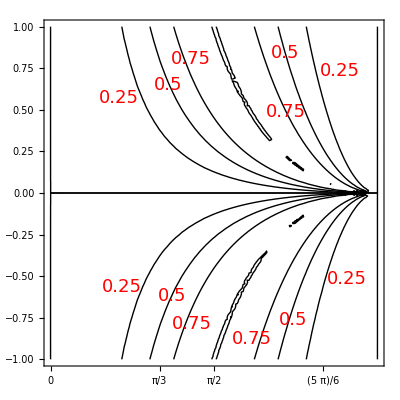

```mathematica
Export["plot_DeltaLR_Zmediated.pdf",%]
```

plot_DeltaLR_Zmediated.pdf

#### Concurrence scattering R L

Basis |R R⟩,|R L⟩,|L R⟩,|L L⟩ . First we take the ket in Eq.(C5b) and normalize it

```mathematica
unnormalizedKetRL={0,(1+Cos[θθ])gR^2,(-1+Cos[θθ])gR gL,0};
```

```mathematica
RLnormalizingFactor=Simplify[1/Sqrt[unnormalizedKetRL.unnormalizedKetRL]];
```

```mathematica
normalizedKetRL=Simplify[RLnormalizingFactor unnormalizedKetRL];
```

```mathematica
alphaRL=normalizedKetRL[[1]];
betaRL=normalizedKetRL[[2]];
gammaRL=normalizedKetRL[[3]];deltaRL=normalizedKetRL[[4]];
```

Concurrence. The |.| not relevant now

```mathematica
concurrenceRL=FullSimplify[2(alphaRL deltaRL-betaRL gammaRL)]
```

-(2 gL gR^3 (-1+Cos[θθ]) (1+Cos[θθ]))/(gL^2 gR^2 (-1+Cos[θθ])^2+gR^4 (1+Cos[θθ])^2)

The numerator is 2 g_L g_R*g_R^2*[-(1-cos^2 θ)]=-2g_L g_R*g_R^2 sin^2 θ, and the denominator is g_R^2*[   (g_L^2(2sin^2(θ/2)))^2+(g_R^2(2cos^2(θ/2)))^2  ]=g_R^2*4(g_L^2 s^4+g_R^2 c^4). Simplify, and verify that it matches Eq. (C6)

Let η_g=g_L/g_R. The Δ_(R L) concurrence is

```mathematica
ΔRLfunction[ηg_,θ_]:=(Abs[ηg] Sin[θ]^2)/(2( Sin[θ/2]^4+ηg^2 Cos[θ/2]^4))
```

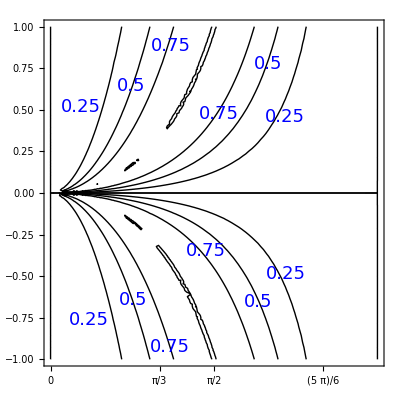

```mathematica
Show[{

ContourPlot[ΔRLfunction[ηg,θ],{θ,0,π},{ηg,-1,1},
FrameLabel->{{MaTeX["g_{R}/g_{L}",FontSize->24],None},{MaTeX["\\theta",FontSize->24],MaTeX["\\Delta_{RL}\\text{ contours}",FontSize->24]}},BaseStyle->fticksStyleMaTeX,
FrameTicksStyle->Directive[20,FontFamily->"TimesNewRoman"],FrameStyle->BlackFrame,FrameTicks->{
{Automatic,Automatic},
{{0,π/6,π/3,π,π/2,2π/3,5π/6,π},Automatic}
},ContourShading->None,Contours->{0.25,0.5,0.75},
ContourLabels->{Function[{x,y,z},Text[Style[   z,FontFamily->"TimesNewRoman",18,Blue   ],{x,y}]
]},
PlotRange->Automatic,PlotRangePadding->0]
,
ContourPlot[ΔRLfunction[ηg,θ],{θ,0,π},{ηg,-1,1},
FrameLabel->{{MaTeX["g_{R}/g_{L}",FontSize->24],None},{MaTeX["\\theta",FontSize->24],MaTeX["\\Delta_{RL}\\text{ contours}",FontSize->24]}},BaseStyle->fticksStyleMaTeX,
FrameTicksStyle->Directive[20,FontFamily->"TimesNewRoman"],FrameStyle->BlackFrame,FrameTicks->{
{Automatic,Automatic},
{{0,π/6,π/3,π,π/2,2π/3,5π/6,π},Automatic}
},ContourShading->None,Contours->{0+10^-6,1-10^-3},
PlotRange->Automatic,PlotRangePadding->0]
,
label0blue,label1blue
}]
```

```mathematica
Export["plot_DeltaRL_Zmediated.pdf",%]
```

plot_DeltaRL_Zmediated.pdf